# Example 5 - Test on the Skewness coefficient of the IG distribution

Data

```mathematica
n= 25;
xmean = 2.1556;
a= 1.701722;
```

Normalizing constant

```mathematica
c = NIntegrate[Sqrt[y^(n-1)/(x^3)]*Exp[-(n/2)*y*(xmean/x^2-2/x+1/a)],{x,0.01,10},{y,0.01,30}];
```

Normalized Posterior distribution

```mathematica
gposterior=(c^(-1))*Sqrt[y^(n-1)/(x^3)]*Exp[-(n/2)*y(xmean/x^2-2/x+1/a)];
```

```mathematica
NIntegrate[gposterior,{x,0.01,10},{y,0.01,30}]
```

1.

## Flat reference function

```mathematica
sknssH=2;
```

```mathematica
yr=x*(3/(sknssH))^2;
```

```mathematica
gprofile=(c^(-1))*Sqrt[yr^(n-1)/(x^3)]*Exp[-(n/2)*yr(xmean/x^2-2/x+1/a)];
```

```mathematica
FindMaximum[gprofile,{x,2}]
```

{0.10728,{x→2.25908}}

Level

```mathematica
kFlat=0.10728
```

0.10728

Region

```mathematica
TbarFlat=DiscretizeRegion[ImplicitRegion[gposterior>kFlat ,{x,y}],{{0.01,10},{0.01,30}},MaxCellMeasure->0.0001]
```

-Graphics-

```mathematica
RegionPlot[TbarFlat]
```

-Graphics-

```mathematica
TbarFlatComplementary=DiscretizeRegion[ImplicitRegion[gposterior<=kFlat,{x,y}],{{0.5,5},{3,15}},MaxCellMeasure->0.01]
```

-Graphics-

Integral

```mathematica
g1[x,y]:=(c^(-1))*Sqrt[y^(n-1)/(x^3)]*Exp[-(n/2)*y(xmean/x^2-2/x+1/a)];
```

```mathematica
Integrate[g1[x,y],{x,y}∈TbarFlat]
```

0.649797

## Jeffreys prior as reference function

Reference function

```mathematica
r=(y*x^3)^(-1/2);
```

Surprise function

```mathematica
s=gposterior/r;
```

```mathematica
sknssH=2;
```

```mathematica
yr=x*(3/(sknssH))^2;
```

Profile function

```mathematica
sprofile=((c^(-1))*Sqrt[yr^(n-1)/(x^3)]*Exp[-(n/2)*yr(xmean/x^2-2/x+1/a)])/(yr*x^3)^(-1/2);
```

```mathematica
FindMaximum[sprofile,{x,3}]
```

{0.847199,{x→2.3304}}

Level

```mathematica
kJeff=0.8471989810991962
```

0.847199

Region

```mathematica
TbarJeff=DiscretizeRegion[ImplicitRegion[s>kJeff ,{x,y}],{{0.01,10},{0.01,30}},MaxCellMeasure->0.0001]
```

-Graphics-

```mathematica
RegionPlot[TbarJeff]
```

-Graphics-

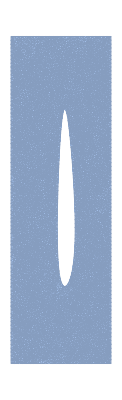

```mathematica
TbarJeffComplementary=DiscretizeRegion[ImplicitRegion[s<=kJeff,{x,y}],{{0.01,4},{2,15}},MaxCellMeasure->0.01]
```

Integral

```mathematica
Integrate[g1[x,y],{x,y}∈TbarJeff]
```

0.691372